```mathematica
Clear[ψ]
```

```mathematica
A[r_]:=f''[r]/2
B[r_]:=-f'[r]/(2r)
CC[r_]:=-f'[r]/(2r)
ψ[r_]:=(1-f[r])/r^2
```

### Eta

```mathematica
eta:=DiagonalMatrix[{-1,1,1,1,1}]
len:=Length[eta]
For[j=0,j<len,j++,For[i=0,i<len,i++,η[i,j]=eta⟦i+1⟧⟦j+1⟧;]]
```

```mathematica
delta[a_,b_]:=KroneckerDelta[a,b]
tau[a_,b_]:=delta[a,0]*delta[0,b]
rho[a_,b_]:=delta[a,1]*delta[1,b]
sigma[a_,b_]:=delta[a,2]*delta[2,b]+delta[a,3]*delta[3,b]+delta[a,4]*delta[4,b]
```

### Tensor de Riemann

```mathematica
RUUDD0[a_,b_,c_,d_]:=2*(-A[r]*2*tau[c,a]*rho[d,b]+B[r]*2*tau[c,a]*sigma[d,b]+CC[r]*2*rho[c,a]*sigma[d,b]+ψ[r]*sigma[c,a]*sigma[d,b])
RUUDD[a_,b_,c_,d_]:=1/8 (RUUDD0[a,b,c,d]-RUUDD0[b,a,c,d]-RUUDD0[a,b,d,c]+RUUDD0[b,a,d,c]+RUUDD0[c,d,a,b]-RUUDD0[d,c,a,b]-RUUDD0[c,d,b,a]+RUUDD0[d,c,b,a])
```

```mathematica
RUUDD[0,1,0,1]
```

-1/2 f''[r]

```mathematica
Clear[a,b,c,d,e,g]
```

```mathematica
RUUUU[a_,b_,c_,d_]:=Sum[η[d,g]*η[c,e]*RUUDD[a,b,e,g],{e,0,len-1},{g,0,len-1}]
```

```mathematica
RUUUU[0,1,0,1]
```

f''[r]/2

```mathematica
RDDDD[a_,b_,c_,d_]:=Sum[η[b,g]*η[a,e]*RUUDD[e,g,c,d],{e,0,len-1},{g,0,len-1}]
```

```mathematica
RDDDD[0,1,0,1]
```

f''[r]/2

```mathematica
Clear[a,b,c,d]
```

```mathematica
K:=Sum[RDDDD[a,b,c,d]*RUUUU[a,b,c,d],{a,0,len-1},{b,0,len-1},{c,0,len-1},{d,0,len-1}]
```

### Invariante Kretschmann

```mathematica
K
```

(12 (1-f[r])^2)/r^4+(3 f'[r]^2)/r^2+(3 (NN[r] f'[r]+2 f[r] NN'[r])^2)/(r^2 NN[r]^2)+(3 f'[r] NN'[r]+NN[r] f''[r]+2 f[r] NN''[r])^2/NN[r]^2

```mathematica
len:=5
α[n_]:=α^(n-1)
h[nmax_]:=Sum[α[n]*ψ[r]^n,{n,1,nmax}]
```

```mathematica
h[3]
```

(1-f[r])/r^2+(α (1-f[r])^2)/r^4+(α^2 (1-f[r])^3)/r^6

```mathematica
Expand[h[3]*r^(len-1)]
```

r^2+α+α^2/r^2-r^2 f[r]-2 α f[r]-(3 α^2 f[r])/r^2+α f[r]^2+(3 α^2 f[r]^2)/r^2-(α^2 f[r]^3)/r^2

```mathematica
f32=f[r]/. Solve[h[3]==m/r^(len-1),f[r],Reals][[1]]
```

Root[m r^2-r^4-r^2 α-α^2+(r^4+2 r^2 α+3 α^2) #1+(-r^2 α-3 α^2) #1^2+α^2 #1^3&,1]

```mathematica
K3=Simplify[(12 (1-f3)^2)/r^4+(6 (D[f3,r])^2)/r^2+D[f3,{r,2}]^2]
```

4 (1/r^4 3 (-1+Root[m r^2-r^4-r^2 α-α^2+(r^4+2 r^2 α+3 α^2) #1+(-r^2 α-3 α^2) #1^2+α^2 #1^3&,1])^2+(6 (-m+2 r^2+α-2 (r^2+α) Root[m r^2-r^4-r^2 α-α^2+(r^4+2 r^2 α+3 α^2) #1+(-r^2 α-3 α^2) #1^2+α^2 #1^3&,1]+α Root[m r^2-r^4-r^2 α-α^2+(r^4+2 r^2 α+3 α^2) #1+(-r^2 α-3 α^2) #1^2+α^2 #1^3&,1]^2)^2)/(r^4+2 r^2 α+3 α^2-2 α (r^2+3 α) Root[m r^2-r^4-r^2 α-α^2+(r^4+2 r^2 α+3 α^2) #1+(-r^2 α-3 α^2) #1^2+α^2 #1^3&,1]+3 α^2 Root[m r^2-r^4-r^2 α-α^2+(r^4+2 r^2 α+3 α^2) #1+(-r^2 α-3 α^2) #1^2+α^2 #1^3&,1]^2)^2+(r^4 (3 r^6 (r^2+2 α)+m^2 α (10 r^2+3 α)-2 m (3 r^6+5 r^4 α-11 r^2 α^2)-(3 r^8-10 m r^4 α+12 r^6 α+3 m^2 α^2+44 m r^2 α^2) Root[m r^2-r^4-r^2 α-α^2+(r^4+2 r^2 α+3 α^2) #1+(-r^2 α-3 α^2) #1^2+α^2 #1^3&,1]+2 r^2 α (3 r^4+11 m α) Root[m r^2-r^4-r^2 α-α^2+(r^4+2 r^2 α+3 α^2) #1+(-r^2 α-3 α^2) #1^2+α^2 #1^3&,1]^2)^2)/(r^4+2 r^2 α+3 α^2-2 α (r^2+3 α) Root[m r^2-r^4-r^2 α-α^2+(r^4+2 r^2 α+3 α^2) #1+(-r^2 α-3 α^2) #1^2+α^2 #1^3&,1]+3 α^2 Root[m r^2-r^4-r^2 α-α^2+(r^4+2 r^2 α+3 α^2) #1+(-r^2 α-3 α^2) #1^2+α^2 #1^3&,1]^2)^6)

```mathematica
α:=0.03
m:=1
```

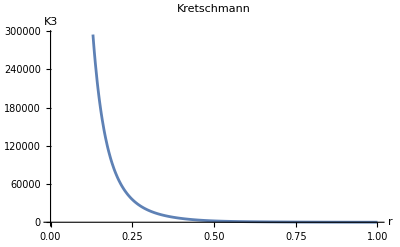

```mathematica
Plot[K3,{r,0,1},PlotLabel->"Kretschmann",AxesLabel->{"r","K3"}]
```

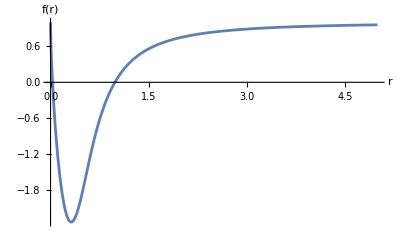

```mathematica
Plot[f32,{r,0,5},AxesLabel->{"r","f(r)"}]
```

```mathematica
Solve[f3==0,r]
```

{}

### Funciones orden n

```mathematica
f1=f[r]/.Simplify[Solve[h[1]==m/r^(len-1),f[r]][[1]]]
```

1-m/r^2

```mathematica
f2=f[r]/. Solve[h[2]==m/r^(len-1),f[r],Reals][[1]]
```

ConditionalExpression[(r^2+2 α)/(2 α)-1/2 √((r^4+4 m α)/α^2), ]

```mathematica
f3=f[r]/. Solve[h[3]==m/r^(len-1),f[r],Reals][[1]]
```

Root[m r^2-r^4-r^2 α-α^2+(r^4+2 r^2 α+3 α^2) #1+(-r^2 α-3 α^2) #1^2+α^2 #1^3&,1]

```mathematica
ToRadicals[f3]
```

-(-r^2 α-3 α^2)/(3 α^2)-(2 2^(1/3) r^4)/(3 (-7 r^6 α^3-27 m r^2 α^4+3 √3 √(3 r^12 α^6+14 m r^8 α^7+27 m^2 r^4 α^8))^(1/3))+((-7 r^6 α^3-27 m r^2 α^4+3 √3 √(3 r^12 α^6+14 m r^8 α^7+27 m^2 r^4 α^8))^(1/3))/(3 2^(1/3) α^2)

```mathematica
Assuming[α>0&&m>0&&r>0,Series[ToRadicals[f3],{r,0,5}]]
```

1-(m^(1/3) r^(2/3))/α^(2/3)+r^2/(3 α)+(2 r^(10/3))/(9 m^(1/3) α^(4/3))-(7 r^(14/3))/(81 (m^(2/3) α^(5/3)))+O[r]^(16/3)

```mathematica
f5=f[r]/. Solve[h[5]==m/r^(len-1),f[r],Reals][[1]]
```

Root[m r^6-r^8-r^6 α-r^4 α^2-r^2 α^3-α^4+(r^8+2 r^6 α+3 r^4 α^2+4 r^2 α^3+5 α^4) #1+(-r^6 α-3 r^4 α^2-6 r^2 α^3-10 α^4) #1^2+(r^4 α^2+4 r^2 α^3+10 α^4) #1^3+(-r^2 α^3-5 α^4) #1^4+α^4 #1^5&,1]

```mathematica
ToRadicals[f5]
```

Root[m r^6-r^8-r^6 α-r^4 α^2-r^2 α^3-α^4+(r^8+2 r^6 α+3 r^4 α^2+4 r^2 α^3+5 α^4) #1+(-r^6 α-3 r^4 α^2-6 r^2 α^3-10 α^4) #1^2+(r^4 α^2+4 r^2 α^3+10 α^4) #1^3+(-r^2 α^3-5 α^4) #1^4+α^4 #1^5&,1]

```mathematica
f7=f[r]/. Solve[h[7]==m/r^(len-1),f[r],Reals][[1]]
```

Root[m r^10-r^12-r^10 α-r^8 α^2-r^6 α^3-r^4 α^4-r^2 α^5-α^6+(r^12+2 r^10 α+3 r^8 α^2+4 r^6 α^3+5 r^4 α^4+6 r^2 α^5+7 α^6) #1+(-r^10 α-3 r^8 α^2-6 r^6 α^3-10 r^4 α^4-15 r^2 α^5-21 α^6) #1^2+(r^8 α^2+4 r^6 α^3+10 r^4 α^4+20 r^2 α^5+35 α^6) #1^3+(-r^6 α^3-5 r^4 α^4-15 r^2 α^5-35 α^6) #1^4+(r^4 α^4+6 r^2 α^5+21 α^6) #1^5+(-r^2 α^5-7 α^6) #1^6+α^6 #1^7&,1]

```mathematica
f8=f[r]/. Solve[h[8]==m/r^(len-1),f[r],Reals][[1]]
```

ConditionalExpression[Root[-m r^12+r^14+r^12 α+r^10 α^2+r^8 α^3+r^6 α^4+r^4 α^5+r^2 α^6+α^7+(-r^14-2 r^12 α-3 r^10 α^2-4 r^8 α^3-5 r^6 α^4-6 r^4 α^5-7 r^2 α^6-8 α^7) #1+(r^12 α+3 r^10 α^2+6 r^8 α^3+10 r^6 α^4+15 r^4 α^5+21 r^2 α^6+28 α^7) #1^2+(-r^10 α^2-4 r^8 α^3-10 r^6 α^4-20 r^4 α^5-35 r^2 α^6-56 α^7) #1^3+(r^8 α^3+5 r^6 α^4+15 r^4 α^5+35 r^2 α^6+70 α^7) #1^4+(-r^6 α^4-6 r^4 α^5-21 r^2 α^6-56 α^7) #1^5+(r^4 α^5+7 r^2 α^6+28 α^7) #1^6+(-r^2 α^6-8 α^7) #1^7+α^7 #1^8&,1], ]

```mathematica
Clear[α,m]
```

```mathematica
α:=0.03
m:=1
```

General::munfl: 5.38084×10^-23 2.46693×10^-308 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 3.77112×10^-139 (-5.12973356614211×10^-181) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1.57065×10^-154 (-1.35805597503384×10^-163) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

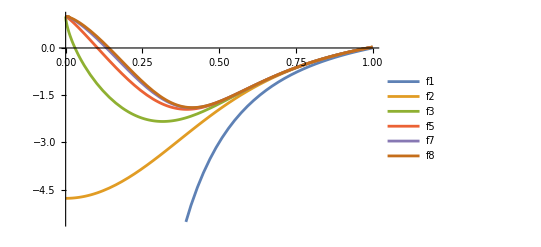

```mathematica
Plot[{f1,f2,f3,f5,f7,f8},{r,0,1},PlotLegends->{"f1","f2","f3","f5","f7","f8"}]
```

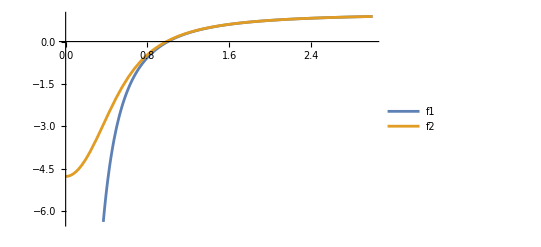

```mathematica
Plot[{f1,f2},{r,0,3},PlotLegends->{"f1","f2"}]
```